# Splines in Action!

Let’s look at some fun examples of using splines!

First, we copy our spline code from last time into a module so we can create splines from data more easily.

```mathematica
Spline[Data_]:=Module[{h,a,L,U,Diag,M,B,c,b,d,Poly,P},
h[n_]:=Data[[n+1]][[1]]-Data[[n]][[1]];(**)
a=Table[Data[[i]][[2]],{i,1,Length[Data]}];
L=DiagonalMatrix[Table[h[i],{i,1,Length[Data]-2}]~Join~{0},-1];
U=DiagonalMatrix[{0}~Join~Table[h[i],{i,2,Length[Data]-1}],1];
Diag=DiagonalMatrix[{1}~Join~Table[2(h[i]+h[i+1]),{i,1,Length[Data]-2}]~Join~{1}];
M=L+U+Diag;
B={0}~Join~Table[(3/h[i+1])(a[[i+2]]-a[[i+1]])-(3/h[i])(a[[i+1]]-a[[i]]),{i,1,Length[Data]-2}]~Join~{0};
c=LinearSolve[M,B];
b=Table[(1/h[i])(a[[i+1]]-a[[i]])-(h[i]/3)(2c[[i]]+c[[i+1]]),{i,1,Length[Data]-1}];
d=Table[(c[[i+1]]-c[[i]])/(3h[i]),{i,1,Length[Data]-1}];
Poly=Table[a[[i]]+b[[i]](x-Data[[i]][[1]])+c[[i]](x-Data[[i]][[1]])^2+d[[i]](x-Data[[i]][[1]])^3,{i,1,Length[Data]-1}];
P=Piecewise[Table[{Poly[[i]],Data[[i]][[1]]≤x≤Data[[i+1]][[1]]},{i,1,Length[Data]-1}]]
]
```

## Example 1

For our first example we will use some of the “curated” data that is accessable from inside Mathematica to analyze population data in France.

```mathematica
CountryData["France",{"Population",{2010,1,1}}][[1]]
```

### Question: How can we use splines to model population data? In particular, suppose we only have access to population data at 5 year intervals. How can we estimate the population between these data points?

To access the population data we can Table over the Wolfram population database and grab the population at every 5th year.
So that we can check the error in our spline estimate we will also grab the population for each year.

```mathematica
FrancePopData=Table[{year,CountryData["France",{"Population",{year,1,1}}][[1]]},{year,1970,2010,5}]
FullPopData=Table[{year,CountryData["France",{"Population",{year,1,1}}][[1]]},{year,1970,2010,1}];
```

Before we get started we can take a look at the data points.

```mathematica
ListPlot[FrancePopData]
```

Since we have a module to generate our spline we can easily compute the polynomials.

```mathematica
FrancePop=Spline[FrancePopData]
```

This isn’t a Pure Function, so if we want to find the population in a particular year we must use a Replacement Rule.

```mathematica
FrancePop/.x->2001
```

We can, of course, plot the original data set along with the spline.

```mathematica
Show[{ListPlot[FrancePopData],Plot[FrancePop,{x,1970,2010}]}]
```

Remember that we actually have access to the yearly population data, so we can see how good our spline approximation is!

```mathematica
Show[{ListPlot[FullPopData],ListPlot[FrancePopData,PlotStyle->{Large,Red}],Plot[FrancePop,{x,1970,2010}]}]
```

This is kind of astonishing! The fit is incredibly good! To see the error quantitatively we can define a function that returns the actual population in a given year...

```mathematica
ActualPop[d_]:=CountryData["France",{"Population",{d,1,1}}][[1]]
```

```mathematica
ActualPop[2001]
```

... and use it to compute the relative error.

```mathematica
RelError[d_]:=Abs[(FrancePop/.x->d)-ActualPop[d]]/ActualPop[d];
```

So, what is the relative error for our estimation of the population in 2001?

```mathematica
RelError[2001]
```

The answer: really small!

Let’s plot the relative error over the entire interval (1970-2010).

```mathematica
ListLinePlot[Table[RelError[d],{d,1970,2010,1}],{Filling->Axis,PlotRange->All}]
```

There is a spike near 1970... why might this be?

## Example 2

Now for an example from statistics. First we should talk a bit about random processes and probability (crash course on the board!).

### Question: If we roll 10 dice, what is the expected sum of the rolls? How can we compute the probability that the sum will be in a certain interval?

```mathematica
numRolls=10; (*Set the number of dice we will roll in each trial*)
numSamples=100000; (*Set the number of trials we will take*)
(*To summarize: we will roll 10 dice 100,000 times*)
box={1,1,1,2,2,2,2,3,4,4,4,6,7}; (*The dice are weighted and this list gives the possible outcomes*)
Roll[n_]:=RandomChoice[box,{n}]; (*Roll[n_] will roll n_ dice*)
Rolls=Table[Roll[numRolls],{i,1,numSamples}]; (*Rolls will perform numSamples trials (which is to roll numRolls dice*)
RollData=Table[Total[Rolls[[i]]],{i,1,numSamples}];(*RollData computes the sum of each trial*)
Data=Tally[RollData]; (*To create our distribution we need to count how many times we got each outcome*)
NormData=Table[{Data[[i,1]],Data[[i,2]]/numSamples},{i,1,Length[Data]}];(*We normalize the data by dividing each sum by numSamples (so that the total area under the curve is 1)*)
ListPlot[NormData]
```

Now we are ready to compute the spline!

```mathematica
SDist=Spline[Sort[NormData]];
Show[{ListPlot[NormData],Plot[SDist,{x,5,50}]}]
```

To answer our first question we can simply find the maximum value of our spline! We could use calculus, but we have Mathematica!

```mathematica
N[Maximize[SDist,x]]
```

To answer our second question we can simply integrate our spline over whatever interval we wish.

```mathematica
N[Integrate[SDist,{x,20,40}]]
```

## Example 3

Our third example is geometric! A random walk is a path in $\mathbb{R}^3$ that is generated by a random process. There are many ways to define them, but we will just use a built in Mathematica function. The type of walks we will look at make a “step” by starting at the origin and randomly choosing a diagonally adjacent vertex (with equal probability) and then walking straight to that vertex.

```mathematica
RandomWalk=RandomFunction[RandomWalkProcess[0.5],{0,3},3];
Graphics3D[Line[Transpose@RandomWalk["States"]],BoxRatios->Automatic]
Transpose@RandomWalk["States"]
```

-Graphics3D-

{{0,0,0},{1,-1,1},{2,0,2},{3,-1,3}}

### Question: If you take a random walk of some fixed length, how far from the origin do you expect to end up? What is the probality that your distance from the origin will be in some interval?

The setup here is basically the same as the last example.

```mathematica
numSteps=100; (*Set the number of steps for each random walk*)
numSamples=10000; (*Set the number of trials*)
GetWalks[n_,steps_]:=Table[RandomFunction[RandomWalkProcess[0.5],{0,steps},3],{i,1,n}]; (*GetWalks will generate n_ random walks of step size steps_*)
```

Now we can generate the walks (this can take a while on this computer).

```mathematica
Walks=Table[GetWalks[20,numSteps],{i,1,numSamples}];
```

For each of the random walks we compute the distance from the end of the walk to the origin.

```mathematica
Distances[Data_]:=Round[Table[N[Sqrt[Sum[Last[Transpose@Data[[j]]["States"]][[i]]^2,{i,1,3}]]],{j,1,Length[Data]}]];
```

We now

```mathematica
Means=Table[Round[N[Mean[Distances[Walks[[i]]]]]],{i,1,numSamples}];
```

```mathematica
Dists=Flatten[Table[Distances[Walks[[i]]],{i,1,numSamples}]];
```

```mathematica
DistanceData=Tally[Dists];
```

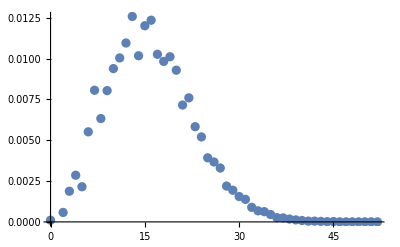

```mathematica
NormDistances=Sort[Table[{DistanceData[[i,1]],DistanceData[[i,2]]/(numSamples*numSteps)},{i,1,Length[DistanceData]}]];
ListPlot[NormDistances]
```

```mathematica
f=Spline[NormDistances];
```

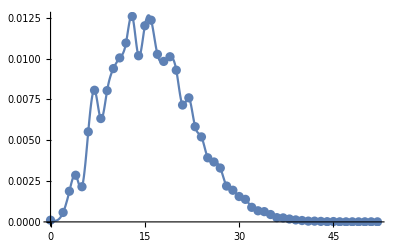

```mathematica
Show[{ListPlot[NormDistances],Plot[f,{x,First[NormDistances[[1]]],Last[NormDistances][[1]]}]}]
```

```mathematica
N[Integrate[f,{x,4,5}]]
```

0.0023806